```mathematica
Covariance
```

```mathematica
SetDirectory["Visual Studio Projects\\smm-bp\\Background"];
Needs["MultivariateStatistics`"]
```

```mathematica
libfile = Import["FormattedCombinatorials_log_ic50.txt","TSV"];
 Rows = Dimensions[libfile][[1]]-1
libvals = libfile[[2;;1+ Rows,3;;22]];
rowmeans = Mean[Transpose[libvals]];
For[row = 1, row≤Rows, row++, libvals[[row, All]]-=rowmeans[[row]];]
(*By normalizing all rows by their rowmeans, the libvals can be interpreted as deviations of an amino acid from the mean interaction. This makes different rows comparable *) 
Covar = Covariance[libvals];
{coeigenval,coeigenvec}= Eigensystem[Covar];
Mean[Transpose[coeigenvec]]
ListPlot[coeigenval, PlotRange->{{0,20.5},{0,1.1}}]
(*All Eigenvectors have sum = zero, as they are relative differences between amino acids due to the normalization. *)
(*This also means that there is an implied Eigenvector (1,1,1,1...),  of coordinated movements of all amino acids. *)
Max[Covar - Transpose[Covar]];
Covar =(Covar + Transpose[Covar]) / 2.0 + .05 ;
{coeigenval2,coeigenvec2}= Eigensystem[Covar];
ListPlot[coeigenval2, PlotRange->{{0,20.5},{0,1.1}}]
(*Adding the transpose ensures exact symmetry, (which due to rounding errors  apparently isn't there even though it should.*) 
(*Adding a constant increases only the Eigenvalue of the Eigenvector (1,1,1,1,1...) to ~ 1.0.  The same effect ccould be achieved by repeating the libvals dataset while adding an offset to all libvals in the repeat. No other eigenvectors are affected. What constant is added is irrelevant for the result. *)
InvCovar = Inverse[Covar] ;
InvCovar = (InvCovar + Transpose[InvCovar])/2.0
Export["InverseCovariance.txt",InvCovar,"TSV"];
(* Again, the adding of transpose is to reach perfect symmetry, which should be but isn't the case for the mathematica output (just a difference of 10^-18..., but not nice) *)
```

Import::nffil: File not found during Import["FormattedCombinatorials_log_ic50.txt", {"TSV"}].

Part::partw: Part 1 of {} does not exist.

-1+{}⟦1⟧

Part::partw: Part 1 of {} does not exist.

Part::span: 2 ;; {} ⟦ 1 ⟧ is not a valid Span specification.  A Span specification should be 1, 2, or 3 integers separated by ;;.  (Any of the integers can be omitted, or replaced with All.)

Covariance::arg1: The first argument must be either a vector or a matrix.

Set::shape: Lists {coeigenval, coeigenvec} and Eigensystem[Covariance[$Failed ⟦ 2 ;; {} ⟦ 1 ⟧, 3 ;; 22 ⟧]] are not the same shape.

Mean[Transpose[coeigenvec]]

ListPlot::lpn: coeigenval is not a list of numbers or pairs of numbers.

ListPlot[coeigenval,PlotRange→{{0,20.5},{0,1.1}}]

Set::shape: Lists {coeigenval2, coeigenvec2} and Eigensystem[0.05  + 0.5\ (Covariance[$Failed ⟦ 2 ;; Part[« 2 »], 3 ;; 22 ⟧] + Transpose[Covariance[$Failed ⟦ Span[« 2 »], Span[« 2 »] ⟧]])] are not the same shape.

ListPlot::lpn: coeigenval2 is not a list of numbers or pairs of numbers.

ListPlot[coeigenval2,PlotRange→{{0,20.5},{0,1.1}}]

0.5 (Inverse[0.05+0.5 (Covariance[$Failed⟦2;;{}⟦1⟧,3;;22⟧]+Transpose[Covariance[$Failed⟦2;;{}⟦1⟧,3;;22⟧]])]+Transpose[Inverse[0.05+0.5 (Covariance[$Failed⟦2;;{}⟦1⟧,3;;22⟧]+Transpose[Covariance[$Failed⟦2;;{}⟦1⟧,3;;22⟧]])]])

```mathematica
SMM - BP
```

```mathematica
(*Import experimental data*)
expfile=Import["mathematica-peptides.csv","CSV"];
H = expfile[[All, 1;;181]];
ineq = expfile[[All, 182]];
meas = expfile[[All, 183]];
Dimensions[meas]
```

{231}

0.316386

{180,180}

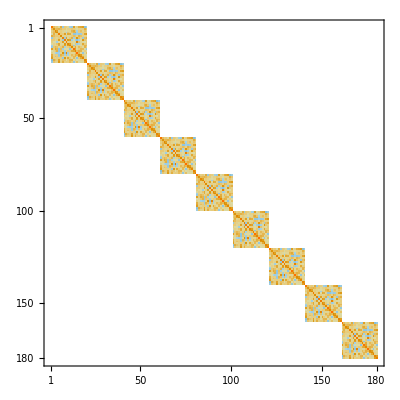
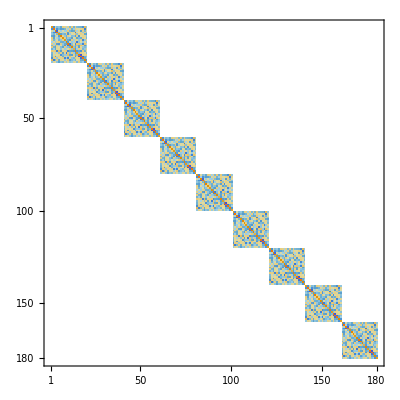

{181,181}

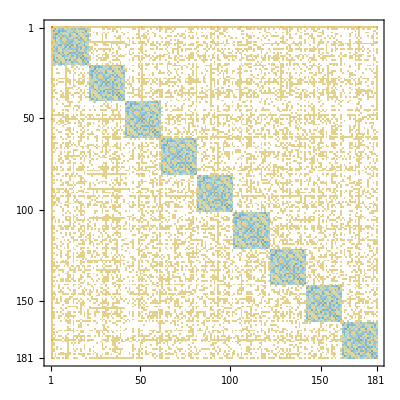

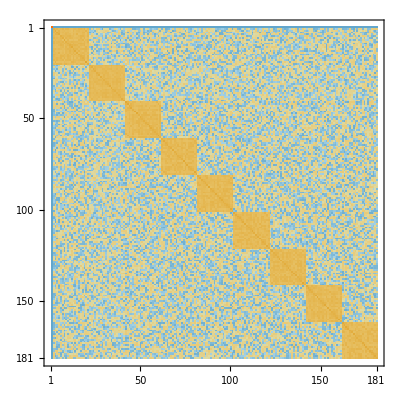

{1.96619,-0.547932,0.0643044,0.0326423,0.231396,0.319533,-0.0107652,-0.052259,-0.185035,-0.141761,-0.0403271,-0.502873,-0.215895,0.927969,0.147312,-0.409926,-0.0779054,-0.0504079,0.0167316,0.212502,0.282695,-0.285154,-0.138455,0.118468,0.169989,0.0114773,0.437766,0.0194631,0.0321737,-0.11656,0.293396,-0.177579,0.0930101,1.1236,-0.13549,-0.505924,-0.0541759,-0.0330854,-0.2807,-0.458191,-0.114032,0.252967,0.0350579,0.606631,0.615599,-0.657749,0.532053,-0.584451,-0.480511,0.157291,0.0878357,-0.466614,0.36464,1.00462,0.413081,-0.154346,0.32384,-0.35371,-0.354088,-0.65451,-0.687643,-0.126259,0.174158,-0.676383,-0.0223867,0.0456618,0.400906,0.225822,0.257048,0.0570699,0.251618,0.229454,-0.129337,0.321313,0.0910535,-0.205804,-0.0632505,-0.111837,-0.00220861,-0.687865,-0.0287735,0.151212,0.0480509,0.301865,0.117118,-0.518676,0.419868,-0.129837,-0.206679,0.214446,-0.0467505,-0.0213348,0.245143,0.0252211,0.0518906,0.1059,0.0392967,0.148868,-0.107803,-0.561792,-0.276007,-0.19086,-0.0961792,0.174021,0.482519,-0.111803,-0.104026,-0.447361,-0.0692637,0.380399,-0.073876,-0.000404175,-0.105863,0.176382,0.274998,0.17832,0.0455721,0.151604,-0.0624759,-0.358908,-0.242796,0.131573,-0.329891,0.198328,-0.0364095,-0.314907,0.0839755,-0.107921,-0.0184824,0.934384,-0.0719359,-0.195537,0.00792585,-0.00578697,-0.257027,0.0296687,0.0386268,0.371486,0.39469,-0.291359,-0.5614,0.398095,-0.343343,0.00672422,0.120139,-0.388455,0.287439,-0.430398,-0.0319156,0.226034,0.329368,-0.20508,0.0484945,0.339636,0.317465,-0.244918,0.0282694,0.14456,0.38301,-0.361415,-0.623709,0.436207,-0.409339,1.05237,1.01504,-1.3042,1.00532,0.026277,-0.748966,1.03959,-0.729936,-1.24837,0.0220105,-0.292349,0.0575107,0.981825,0.742232,0.496058,-0.16684,-0.978068,-0.996376}

{0,2,21,-1.99007×10^-13}

{1,22,41,1.58346×10^-13}

{2,42,61,1.51545×10^-13}

{3,62,81,-2.84526×10^-13}

{4,82,101,-1.60816×10^-13}

{5,102,121,3.99708×10^-13}

{6,122,141,-5.51559×10^-13}

{7,142,161,-1.35225×10^-13}

{8,162,181,-2.5524×10^-13}

```mathematica
(*construct covariance matrix for 9-ner peptides*)
lambda= Sqrt[.1001] (* lambda =  standard deviation of the error distribution *)
c= Table[0,{i,180},{j,180}];
Dimensions[c]
For[pos=0, pos<9, pos++, c[[1+pos*20;;20+pos*20,1+pos*20;;20+pos*20]]=Covar;];
cinverse = Inverse[c] *lambda^2;
{MatrixPlot[c], MatrixPlot[cinverse] }
(* now construct the analytical solution of SMM-BP for the peptides, measurements covariance and lambda given *) 
minv = Transpose[H].H;
Dimensions[minv]
minv[[2;;181,2;;181]]+=cinverse;
MatrixPlot[minv]
minvinv=Inverse[minv];
MatrixPlot[minvinv]
y= minvinv.Transpose[H].meas
For[i=0, i<9, i++, Print[{i,2+i*20, 1+(i+1)*20 ,Sum[y[[j]],{j,2+i*20, 1+(i+1)*20}]}]]
(* The  solutions have sum 0 at each position*)
```

```mathematica
(* Compare the results if a constant offset is added to the Covariance matrix *)
c2= Table[0,{i,180},{j,180}];
For[pos=0, pos<9, pos++, c2[[1+pos*20;;20+pos*20,1+pos*20;;20+pos*20]]=Covar + 10;];
cinverse2 = Inverse[c2] *lambda^2;
minv2 = Transpose[H].H;
minv2[[2;;181,2;;181]]+=cinverse2;
minvinv2=Inverse[minv2];
y2= minvinv2.Transpose[H].meas
Max[Abs[y - y2]]
Max[Abs[minvinv2-minvinv]]
(* Should show no difference in the solution but in the mininv *)
```

{1.96619,-0.547932,0.0643044,0.0326423,0.231396,0.319533,-0.0107652,-0.052259,-0.185035,-0.141761,-0.0403271,-0.502873,-0.215895,0.927969,0.147312,-0.409926,-0.0779054,-0.0504079,0.0167316,0.212502,0.282695,-0.285154,-0.138455,0.118468,0.169989,0.0114773,0.437766,0.0194631,0.0321737,-0.11656,0.293396,-0.177579,0.0930101,1.1236,-0.13549,-0.505924,-0.0541759,-0.0330854,-0.2807,-0.458191,-0.114032,0.252967,0.0350579,0.606631,0.615599,-0.657749,0.532053,-0.584451,-0.480511,0.157291,0.0878357,-0.466614,0.36464,1.00462,0.413081,-0.154346,0.32384,-0.35371,-0.354088,-0.65451,-0.687643,-0.126259,0.174158,-0.676383,-0.0223867,0.0456618,0.400906,0.225822,0.257048,0.0570699,0.251618,0.229454,-0.129337,0.321313,0.0910535,-0.205804,-0.0632505,-0.111837,-0.00220861,-0.687865,-0.0287735,0.151212,0.0480509,0.301865,0.117118,-0.518676,0.419868,-0.129837,-0.206679,0.214446,-0.0467505,-0.0213348,0.245143,0.0252211,0.0518906,0.1059,0.0392967,0.148868,-0.107803,-0.561792,-0.276007,-0.19086,-0.0961792,0.174021,0.482519,-0.111803,-0.104026,-0.447361,-0.0692637,0.380399,-0.073876,-0.000404175,-0.105863,0.176382,0.274998,0.17832,0.0455721,0.151604,-0.0624759,-0.358908,-0.242796,0.131573,-0.329891,0.198328,-0.0364095,-0.314907,0.0839755,-0.107921,-0.0184824,0.934384,-0.0719359,-0.195537,0.00792585,-0.00578697,-0.257027,0.0296687,0.0386268,0.371486,0.39469,-0.291359,-0.5614,0.398095,-0.343343,0.00672422,0.120139,-0.388455,0.287439,-0.430398,-0.0319156,0.226034,0.329368,-0.20508,0.0484945,0.339636,0.317465,-0.244918,0.0282694,0.14456,0.38301,-0.361415,-0.623709,0.436207,-0.409339,1.05237,1.01504,-1.3042,1.00532,0.026277,-0.748966,1.03959,-0.729936,-1.24837,0.0220105,-0.292349,0.0575107,0.981825,0.742232,0.496058,-0.16684,-0.978068,-0.996376}

4.41582×10^-11

899.101

```mathematica
SolveCoSMM[Peptides_, meas_, sigma_]:=
Module[{W, error,ExpFit,PCov, CoSMM, N}, 
W:= Table[Subscript[w, i],{i,181}];
error = Peptides.W- meas;
N = Dimensions[meas][[1]];
ExpFit= Product[PDF[NormalDistribution[0,sigma], error[[i]]],{i,1,N}];
PCov[x_]:=PDF[MultinormalDistribution[Table[0,{i,20}],Covar],x];
CoSMM[x_]:=Product[PCov[x[[2+20*pos;;21+20*pos]]],{pos,0,8}];
Maximize[(ExpFit * CoSMM[W]) , W]
]
SetSplit[Peptides_, meas_, cv_Integer, cvNum_Integer]:=
Module[{trainpep, trainmeas, blindpep, blindmeas,N,i},
N = Dimensions[meas][[1]];
trainpep={};
trainmeas = {};
blindpep={};
blindmeas = {};
For[i=1, i<=N, i++,
If[ Mod[(i-1),cvNum]==cv,
AppendTo[blindpep,Peptides[[i]]];AppendTo[blindmeas,meas[[i]]];, 
AppendTo[trainpep,Peptides[[i]]];AppendTo[trainmeas,meas[[i]]];]];
{trainpep, trainmeas, blindpep, blindmeas}
]
crossValidate[Peptides_,meas_,sigma_,cvNum_Integer]:=
Module[{cv, t, tm, b, bm, sol,W, p,pred, x},
pred ={}; 
x={};
W:= Table[Subscript[w, i],{i,181}];
For[cv=0, cv<cvNum, cv++,
{t, tm, b, bm}=SetSplit[Peptides,meas,cv,cvNum];
PrintTemporary[cv];sol=SolveCoSMM[t,tm,sigma];
p = b.(W/.sol[[2]]);
pred=Join[pred,p];
x=Join[x,bm];
];
{x,pred}
]
optimalSigma[Peptides_,meas_,smin_,smax_,sstep_, cvNum_Integer]:=
Module[{p,m, corr, dist, sigma,s, vals},
corr ={};
dist = {};
sigma = {};
vals ={};
For[s=smin, s<smax, s*=sstep,
{m,p} = crossValidate[Peptides,meas,s,cvNum];
sigma=Append[sigma,s];
vals=Append[vals,{m,p}];
corr=Append[corr, Correlation[m,p] * Correlation[m,p]];
dist=Append[dist,(m-p).(m-p)];
Print[sigma,corr,dist];
];
]
```

```mathematica
x = SolveCoSMM[H,meas,lambda];
W:= Table[Subscript[w, i],{i,181}];
y2 = W /. x[[2]];
Max[Abs[y - y2]] (* Evaluates how far the numerical is from the analytical solution *)
```

3.9746×10^-13

```mathematica
(*Run Cross Validation on this, determine optimal Lambda, compare to CPP solution *)
CPPlambda = Sqrt[0.264305]
optimalSigma[H,meas,CPPlambda,1,10,5]
```

0.514106

{0.514106}{0.540641}{121.213}

```mathematica
optimalSigma[H,meas,0.1,1,2,5]
optimalSigma[H,meas,CPPlambda,1,10,5]
optimalSigma[H,meas,CPPlambda+0.01,1,10,5]
optimalSigma[H,meas,CPPlambda-0.01,1,10,5]
```

```mathematica
(* Redo the functions to include position specific lambda, for convencience and confusion, use lambda, not lambda^2 *)
SolveCoSMM2[Peptides_, meas_, sigma_]:=
Module[{W, error,ExpFit,PCov, CoSMM, N}, 
W:= Table[Subscript[w, i],{i,181}];
error = Peptides.W- meas;
N = Dimensions[meas][[1]];
ExpFit= Product[PDF[NormalDistribution[0,1], error[[i]]],{i,1,N}];
PCov[x_, l_]:=PDF[MultinormalDistribution[Table[0,{i,20}], l^-2 * Covar],x];
CoSMM[x_]:=Product[
PDF[ MultinormalDistribution[ Table[0,{i,20}] , sigma[[pos+1]]^-2 * Covar], x[[2+20*pos;;21+20*pos]]]
,{pos,0,8}];
Maximize[(ExpFit * CoSMM[W]) , W]
]
crossValidate2[Peptides_,meas_,sigma_,cvNum_Integer]:=
Module[{cv, t, tm, b, bm, sol,W, p,pred, x, dist},
pred ={}; 
x={};
W:= Table[Subscript[w, i],{i,181}];
For[cv=0, cv<cvNum, cv++,
PrintTemporary[{"CV", cv}];
{t, tm, b, bm}=SetSplit[Peptides,meas,cv,cvNum];
sol=SolveCoSMM2[t,tm,sigma];
p = b.(W/.sol[[2]]);
pred=Join[pred,p];
x=Join[x,bm];
];
dist = ((x-pred).(x-pred)) / Length[x]
]
Distance2[sigma_]:= crossValidate2[H,meas,sigma,5]
```

```mathematica
l = Table[CPPlambda,{i,9}]
Distance2[l]
```

{0.514106,0.514106,0.514106,0.514106,0.514106,0.514106,0.514106,0.514106,0.514106}

0.52473

```mathematica
For[pos=1, pos≤9, pos++, 
l2=l;
l2[[pos]]+=0.001;
d2 = Distance2[l2];
Print[(d2-0.52473)/0.001];
]
```

-0.0686885

0.0452462

0.0156438

0.0285112

-0.0581824

-0.0250599

-0.0683745

-0.081171

0.216083

```mathematica
lopt={0.561222,0.155626,0.32379,0.166698,1.12112,0.251857,2.99055,0.777421,0.080459};
Distance2[Sqrt[lopt]]
```

0.441571

```mathematica
(*Gradient at optimum*)
For[pos=1, pos≤9, pos++, 
l2=Sqrt[lopt];
l2[[pos]]+=0.001;
d2 = Distance2[l2];
Print[{d2, (d2-0.44157149072845525)/0.001}];
]
```

{0.441572,0.0000923039}

{0.441572,0.000104651}

{0.441572,0.00010551}

{0.441572,0.0000172368}

{0.441572,0.0000142444}

{0.441572,0.0000382668}

{0.441571,-0.0000121942}

{0.441572,0.0000158253}

{0.441572,0.000488736}